# Limaçon

### Author

Eric W. Weisstein
June 6, 2014

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PlaneCurves/Limacon.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Limacon.html.

©2014 Wolfram Research, Inc. except for portions noted otherwise

## Plot

```mathematica
MakeBoxes[b_ +a_ Cos[z_Symbol],TraditionalForm]:=RowBox[{MakeBoxes[b,TraditionalForm],"+",RowBox[{MakeBoxes[a,TraditionalForm]," ","cos"," ",MakeBoxes[z,TraditionalForm]}]}]
MakeBoxes[b_ + Cos[z_Symbol],TraditionalForm]:=RowBox[{MakeBoxes[b,TraditionalForm],"+",RowBox[{"cos"," ",MakeBoxes[z,TraditionalForm]}]}]
MakeBoxes[Equal[x_,y_],TraditionalForm]:=RowBox[{MakeBoxes[x,TraditionalForm],"=",MakeBoxes[y,TraditionalForm]}]
MakeBoxes[Cos[z_Symbol],TraditionalForm]:=RowBox[{"cos",MakeBoxes[z,TraditionalForm]}]
```

```mathematica
Show[GraphicsArray[
PolarPlot[#+Cos[t],{t,0,If[#==0,1,2]π},PlotStyle->Red,
PlotLabel->TraditionalForm[r==#+ Cos[θ]],
Ticks->None,
DisplayFunction->Identity]&/@{2,1.3,1,.5,0}
]]
```

⁃GraphicsArray⁃

```mathematica
Show[Block[{$DisplayFunction=Identity},
Table[PolarPlot[a+Cos[t],{t,0,2π},
Ticks->None,PlotStyle->Hue[a/2]],{a,0,2,.1}]
]]
```

⁃Graphics⁃

```mathematica
(b+a Cos[t])
```

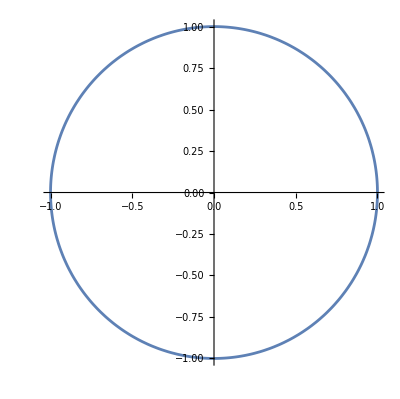
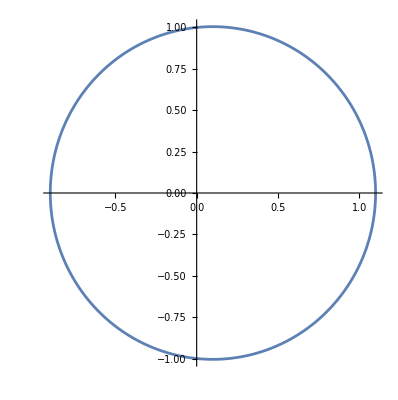
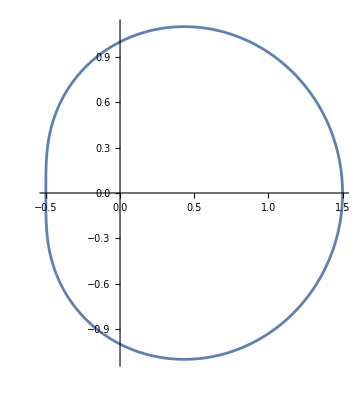
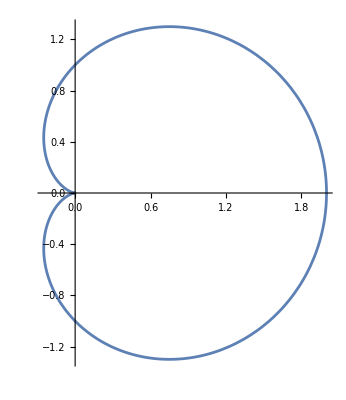
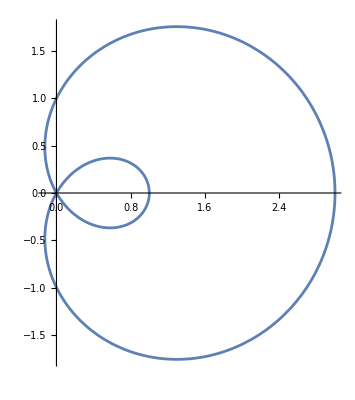
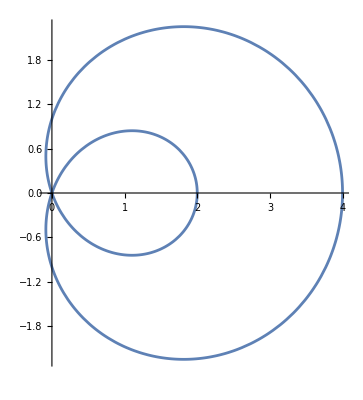

```mathematica
ParametricPlot[(1+# Cos[t]){Cos[t],Sin[t]},{t,0,2π}]&/@{0,.1,.5,1,2,3}
```

```mathematica
(b+a Cos[t])
```

```mathematica
{a==b cusp, a/b>1 acnode, a/b<1 crunode,b==0 None}
```

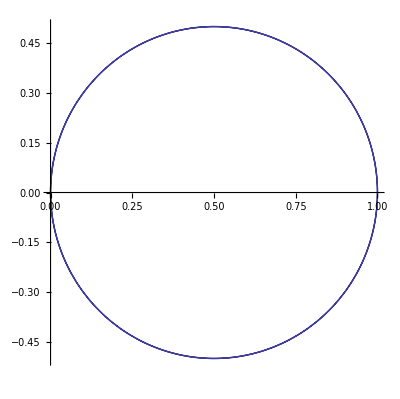
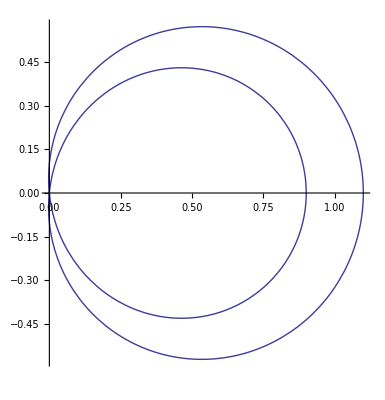
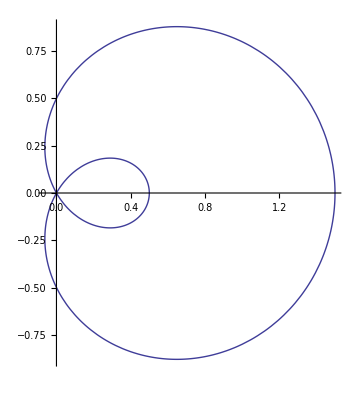
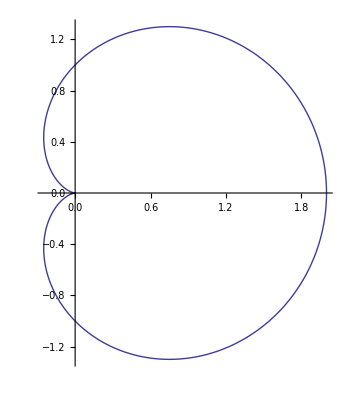
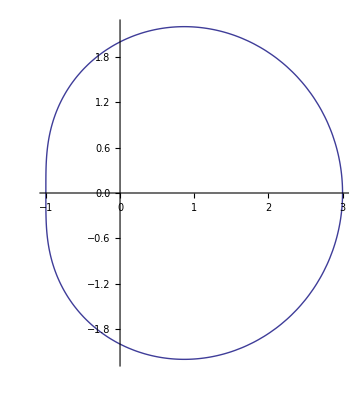
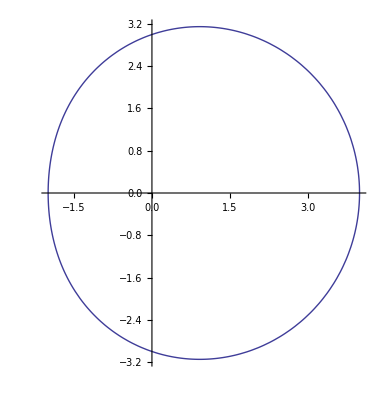

```mathematica
ParametricPlot[(#+Cos[t]){Cos[t],Sin[t]},{t,0,2π}]&/@{0,.1,.5,1,2,3}
```

## Equations

### Cartesian

```mathematica
Factor/@GroebnerBasis[Append[Thread[{x,y}==(b+a Cos[t]) {Cos[t],Sin[t]}],Cos[t]^2+Sin[t]^2==1],{x,y},{Cos[t],Sin[t]}]
```

{a^2 x^2-b^2 x^2-2 a x^3+x^4-b^2 y^2-2 a x y^2+2 x^2 y^2+y^4}

```mathematica
FullSimplify[%]
```

{(a-b-x) (a+b-x) x^2-(b^2+2 (a-x) x) y^2+y^4}

```mathematica
eqn=a^2 x^2-b^2 x^2-2 a x^3+x^4-b^2 y^2-2 a x y^2+2 x^2 y^2+y^4;
```

```mathematica
eqn/.{x->0,y->0}
```

0

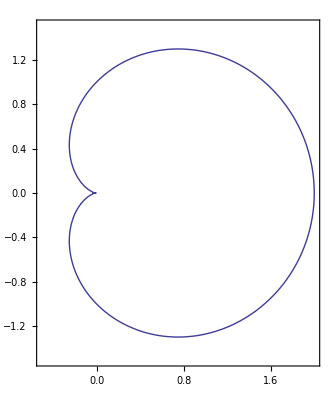

```mathematica
With[{a=1,b=1},
ContourPlot[a^2 x^2-b^2 x^2-2 a x^3+x^4-b^2 y^2-2 a x y^2+2 x^2 y^2+y^4==0,{x,-.5,2},{y,-1.5,1.5},Contours->{0},AspectRatio->Automatic,MaxRecursion->3]]
```

## Properties

```mathematica
curve=(b+a Cos[t]) {Cos[t],Sin[t]};
```

### ArcLength

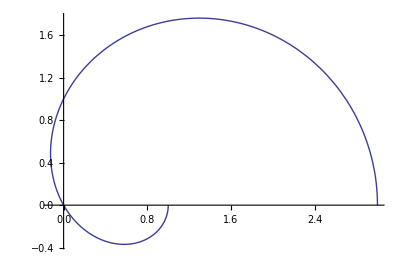

```mathematica
With[{a=2,b=1},ParametricPlot[(b+a Cos[t]) {Cos[t],Sin[t]},{t,0,π}]]
```

```mathematica
ArcLength[(b+a Cos[t]) {Cos[t],Sin[t]},t,Assumptions->a>0&&b>0&&t>0]
```

2 (a+b) EllipticE[t/2,(4 a b)/(a+b)^2]

```mathematica
Limit[%,t->2π]
```

4 (a+b) EllipticE[(4 a b)/(a+b)^2]

```mathematica
4 (a+b) EllipticE[(4 a b)/(a+b)^2]/.b->0
```

2 a π

#### Inner Loop

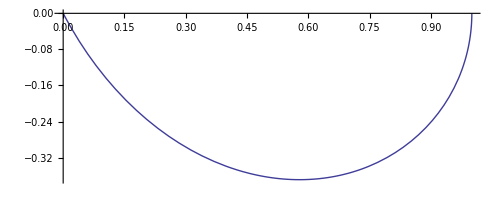

```mathematica
With[{a=2,b=1},ParametricPlot[(b+a Cos[t]) {Cos[t],Sin[t]},{t,π-ArcCos[b/a],π}]]
```

```mathematica
s1=With[{θ0=ArcCos[b/a]},ArcLength[b+a Cos[θ],{θ,π-θ0,π},Assumptions->0<b<a]]
```

2 (a+b) (EllipticE[(4 a b)/(a+b)^2]-EllipticE[1/4 (π-2 ⅈ Log[(ⅈ b+√(a^2-b^2))/a]),(4 a b)/(a+b)^2])

```mathematica
FullSimplify[s1/.l_Log:>ComplexExpand[l,TargetFunctions->{Re,Im}],0<b<a]
```

2 (a+b) (EllipticE[(4 a b)/(a+b)^2]-EllipticE[1/4 (π+2 ArcTan[√(a^2-b^2),b]),(4 a b)/(a+b)^2])

#### Outer Envelope

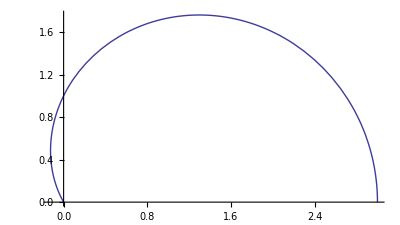

```mathematica
With[{a=2,b=1},ParametricPlot[(b+a Cos[t]) {Cos[t],Sin[t]},{t,0,π-ArcCos[b/a]}]]
```

```mathematica
s2=With[{θ0=ArcCos[b/a]},ArcLength[b+a Cos[θ],{θ,0,π-θ0},Assumptions->0<b<a]]
```

2 (a+b) EllipticE[1/4 (π-2 ⅈ Log[(ⅈ b+√(a^2-b^2))/a]),(4 a b)/(a+b)^2]

```mathematica
FullSimplify[s2/.l_Log:>ComplexExpand[l,TargetFunctions->{Re,Im}],0<b<a]
```

2 (a+b) EllipticE[1/4 (π+2 ArcTan[√(a^2-b^2),b]),(4 a b)/(a+b)^2]

#### Total

```mathematica
2FullSimplify[s1+s2/.l_Log:>ComplexExpand[l,TargetFunctions->{Re,Im}],0<b<a]
```

4 (a+b) EllipticE[(4 a b)/(a+b)^2]

```mathematica
Limit[2s1+s2,b->a]
```

$Aborted

### Area

```mathematica
Assuming[a>0&&b>0,Area[curve,{t,0,2π}]]//Timing
```

{0.55892,1/2 (a^2+2 b^2) π}

#### Check1

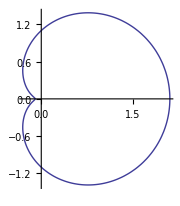

```mathematica
ParametricPlot[curve/.{a->1,b->1.1},{t,0,2π},ImageSize->Small]
```

```mathematica
1/2 (a^2+2 b^2) π/.{a->1,b->1.1}
```

5.37212

```mathematica
1/2 (3 b Sqrt[(a-b) (a+b)]+a^2 Pi+2 b^2 Pi-(a^2+2 b^2) ArcCos[b/a])/.{a->1,b->1.1}
```

5.37212-0.00237673 ⅈ

#### Check2

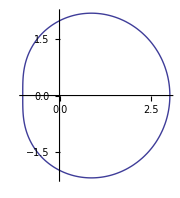

```mathematica
ParametricPlot[curve/.{a->1,b->2},{t,0,2π},ImageSize->Small]
```

```mathematica
1/2 (a^2+2 b^2) π/.{a->1,b->12}
```

(289 π)/2

```mathematica
1/2 (3 b Sqrt[(a-b) (a+b)]+a^2 Pi+2 b^2 Pi-(a^2+2 b^2) ArcCos[b/a])/.{a->1,b->2}
```

1/2 (6 ⅈ √3+9 π-9 ArcCos[2])

### AreaInertiaTensor

```mathematica
Assuming[a>0&&b>0,AreaInertiaTensor[curve,{t,0,2π}]]//Timing
```

{8.82066,{{1/32 (a^4+12 a^2 b^2+8 b^4) π,0},{0,1/32 (5 a^4+36 a^2 b^2+8 b^4) π}}}

### Centroid

```mathematica
Assuming[a>0&&b>0,Centroid[curve,{t,0,2π}]]//Timing
```

{3.48647,{0,(a (a^2+4 b^2))/(2 (a^2+2 b^2))}}

### Curvature

#### Parametric

```mathematica
FullSimplify[Curvature[curve,t]]
```

(2 a^2+b^2+3 a b Cos[t])/((a^2+b^2+2 a b Cos[t])^(3/2))

#### Polar

```mathematica
FullSimplify[Curvature[b+a Cos[q],q],a>0&&b>0&&0<q<2π]
```

(2 a^2+b^2+3 a b Cos[q])/((a^2+b^2+2 a b Cos[q])^(3/2))

#### Implicit

```mathematica
SortBy[FullSimplify[Curvature[eqn,{x,y}],a>0&&b>0&&(x|y)∈Reals],ByteCount]
```

{(-2 a^4 x^2+b^4 (x^2+y^2)+2 a^3 x (x^2+y^2)+4 a b^2 x (x^2+y^2)+a^2 b^2 (x^2+2 y^2))/(b (x^2 (-a^2+b^2+2 a x)+(a^2+b^2+2 a x) y^2)^(3/2)),(-8 (b^2+2 (a-x) x-6 y^2) ((b^2-(a-2 x) (a-x)) x+(a-2 x) y^2)^2-32 (a-2 x) y^2 (x (a^2-b^2-3 a x+2 x^2)-(a-2 x) y^2) (b^2+2 a x-2 (x^2+y^2))+8 y^2 (a^2-b^2-6 a x+6 x^2+2 y^2) (b^2+2 a x-2 (x^2+y^2))^2)/((2 x (a^2-b^2-3 a x+2 x^2)-2 (a-2 x) y^2)^2+4 y^2 (b^2+2 a x-2 (x^2+y^2))^2)^(3/2)}

```mathematica
ByteCount/@%
```

{2728,5824}

### Slope

```mathematica
Slope[(b+a Cos[t]) {Cos[t],Sin[t]},t]//FullSimplify
```

-((b Cos[t]+a Cos[2 t]) Csc[t])/(b+2 a Cos[t])

```mathematica
Slope[b+a Cos[q],q]//FullSimplify
```

-((b Cos[q]+a Cos[2 q]) Csc[q])/(b+2 a Cos[q])

```mathematica
Slope[a^2 x^2-b^2 x^2-2 a x^3+x^4-b^2 y^2-2 a x y^2+2 x^2 y^2+y^4==0,{x,y}]//FullSimplify
```

{((b^2-(a-2 x) (a-x)) x+(a-2 x) y^2)/(y (-b^2+2 (-a x+x^2+y^2))),((b^2-(a-2 x) (a-x)) x+(a-2 x) y^2)/(y (-b^2+2 (-a x+x^2+y^2)))}

### SpecialAffineCurvature

```mathematica
FullSimplify[SpecialAffineCurvature[curve,t],a>0&&b>0&&0<t<2π]
```

(16 a^4+15 a^2 b^2+b^4+2 a b ((17 a^2+4 b^2) Cos[t]+5 a b Cos[2 t]))/((2 a^2+b^2+3 a b Cos[t])^(8/3))

### Tangential Angle

```mathematica
TangentialAngle[curve,t,Assumptions->a>0&&b>0&&t>0]
```

If[a^2+b^2+2 a b Cos[t]≠0&&2 a b+(a+b)^2 Re[1/(-1+Cos[t])]≤0&&((a^2+b^2+2 a b Cos[t])/(2 a b-2 a b Cos[t])∉Reals||(a^2+b^2+2 a b Cos[t]) Re[1/(-2 a b+2 a b Cos[t])]≤0),(3 t)/2-((-a+b) π)/(2 Abs[a-b])-ArcTan[((a+b) Cot[t/2])/(a-b)],Integrate[(t (2 a^2+b^2+3 a b Cos[t t]))/(a^2+b^2+2 a b Cos[t t]),{t,0,1},Assumptions→a>0&&b>0&&!(a^2+b^2+2 a b Cos[t]≠0&&(Csc[t/2]^2∉Reals||Re[Csc[t/2]^2]≤0||((a+b)^2 Re[Csc[t/2]^2]≥4 a b&&(Cos[t]∉Reals||2 a b+(a+b)^2 Re[1/(-1+Cos[t])]≤0)))&&((a^2+b^2+2 a b Cos[t])/(-2 a b+2 a b Cos[t])∉Reals||Re[(a^2+b^2+2 a b Cos[t])/(-2 a b+2 a b Cos[t])]≤0||(Re[(a^2+b^2+2 a b Cos[t])/(-2 a b+2 a b Cos[t])]≥1&&(((a^2+b^2+2 a b Cos[t]) Csc[t/2]^2)/(a b)∉Reals||4+Re[((a^2+b^2+2 a b Cos[t]) Csc[t/2]^2)/(a b)]≤0))))]]

## Area

```mathematica
With[{b=.5,a=1},
Show[GraphicsArray[
PolarPlot[b+a Cos[θ],Evaluate[{θ,Sequence@@#}],
AspectRatio->Automatic,PlotRange->{{-.2,1.7},{-1,1}},
Ticks->None,PlotStyle->Red,DisplayFunction->Identity]&/@{
{Pi-ArcCos[b/a],Pi+ArcCos[b/a]},
{-Pi+ArcCos[b/a],Pi-ArcCos[b/a]},
{0,2π}
}
]]]
```

⁃GraphicsArray⁃

### Inner Loop

```mathematica
With[{b=.5,a=1},
PolarPlot[b+a Cos[θ],{θ,Pi-ArcCos[b/a],Pi+ArcCos[b/a]},
Ticks->None,PlotStyle->Red
]
]
```

⁃Graphics⁃

```mathematica
Solve[0==b+a Cos[θ],θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found. (More…)

{{θ→-ArcCos[-b/a]},{θ→ArcCos[-b/a]}}

```mathematica
With[{b=.5,a=1},{{θ->-ArcCos[-b/a]},{θ->ArcCos[-b/a]}}]
```

{{θ→-2.0944},{θ→2.0944}}

```mathematica
area=FullSimplify[Integrate[(b+a Cos[θ])^2,{θ,Pi-ArcCos[b/a],Pi+ArcCos[b/a]}],0<b<a]/2
```

1/2 (-3 b √((a-b) (a+b))+(a^2+2 b^2) ArcCos[b/a])

```mathematica
area=FullSimplify[Integrate[(b+a Cos[θ])^2,{θ,Pi-ArcCos[b/a],Pi}],0<b<a]
```

1/2 (-3 b √((a-b) (a+b))+(a^2+2 b^2) ArcCos[b/a])

### Outer Envelope

```mathematica
With[{b=.5,a=1},
PolarPlot[b+a Cos[θ],{θ,-Pi+ArcCos[b/a],Pi-ArcCos[b/a]},
Ticks->None,PlotStyle->Red
]
]
```

⁃Graphics⁃

```mathematica
area2=FullSimplify[Integrate[(b+a Cos[θ])^2,{θ,-(Pi-ArcCos[b/a]),Pi-ArcCos[b/a]}],0<b<a]/2
```

1/2 (3 b √((a-b) (a+b))+a^2 π+2 b^2 π-(a^2+2 b^2) ArcCos[b/a])

```mathematica
area2=FullSimplify[Integrate[(b+a Cos[θ])^2,{θ,0,Pi-ArcCos[b/a]}],0<b<a]
```

1/2 (3 b √((a-b) (a+b))+a^2 π+2 b^2 π-(a^2+2 b^2) ArcCos[b/a])

### Between Loops

```mathematica
darea=FullSimplify[area2-area,0<b<a]
```

3 b √((a-b) (a+b))+(a^2+2 b^2) ArcSin[b/a]

### b=a/2

```mathematica
FullSimplify[{area,darea,area2}/.b->a/2,a>0]
```

{1/8 a^2 (-3 √3+2 π),1/4 a^2 (3 √3+π),1/8 a^2 (3 √3+4 π)}

## Envelope

```mathematica
LimaconCircle[i_,n_,x_]:=Module[{k=(Pi/2+2Pi i/n)//N},Circle[{Cos[k],Sin[k]},Sqrt[(Cos[k]-x)^2+Sin[k]^2]]]

LimaconEnvelope[n_,x_]:=Module[{i},Table[LimaconCircle[i,n,x],{i,1,n}]]

LimaconCenter:=Circle[{0,0},1]
```

```mathematica
Show[Graphics[{LimaconEnvelope[20,1],{Thickness[.015],LimaconCenter}}],
  AspectRatio->Automatic]
```

⁃Graphics⁃

```mathematica
Show[GraphicsArray[{
Show[Graphics[{LimaconEnvelope[20,.4],{Thickness[.015],LimaconCenter}}],
  AspectRatio->Automatic,DisplayFunction->Identity],
Show[Graphics[{LimaconEnvelope[20,.8],{Thickness[.015],LimaconCenter}}],
  AspectRatio->Automatic,DisplayFunction->Identity],
  Show[Graphics[{LimaconEnvelope[20,1],{Thickness[.015],LimaconCenter}}],
  AspectRatio->Automatic,DisplayFunction->Identity],
  Show[Graphics[{LimaconEnvelope[20,1.5],{Thickness[.015],LimaconCenter}}],
  AspectRatio->Automatic,DisplayFunction->Identity]}]]
```

⁃GraphicsArray⁃

## Vector Properties

```mathematica
parm=(b+a Cos[t]) {Cos[t],Sin[t]};
assum=a>0&&b>0&&0<t<2π;
xform={Abs[x_]^(n_/;Mod[n,2]==0):>x^n};
```

#### VectorLength

```mathematica
Assuming[assum,FullSimplify[Norm[parm]/.xform]]
```

Abs[b+a Cos[t]]

#### NormalVector

```mathematica
Assuming[assum,FullSimplify[NormalVector[parm,t]/.xform]]
```

{-(b Cos[t]+a Cos[2 t])/(√(a^2+b^2+2 a b Cos[t])),-((b+2 a Cos[t]) Sin[t])/(√(a^2+b^2+2 a b Cos[t]))}

#### TangentVector

```mathematica
Assuming[assum,FullSimplify[TangentVector[parm,t]/.xform]]
```

{-((b+2 a Cos[t]) Sin[t])/(√(a^2+b^2+2 a b Cos[t])),(b Cos[t]+a Cos[2 t])/(√(a^2+b^2+2 a b Cos[t]))}